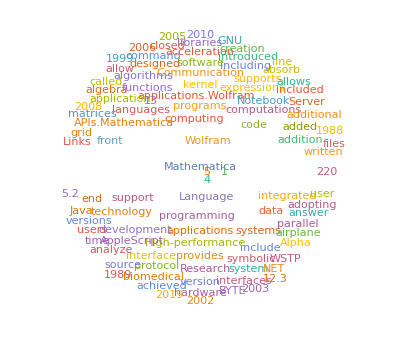

```mathematica
WordCloud[WikipediaData["Mathematica"]]
```

```mathematica
Crash Course in Mathematica for Graduate Students
```

## Introduction Lesson 1

In MATHEMATICA we can solve symbolic expressions

```mathematica
Solve[a x^2+b x+c==0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

and solve maths problem like ODEs

```mathematica
DSolve[{x''[t]+3 x'[t]+2x[t]==0, 
x[0]==1, x'[0]==0}, x[t], t ]
```

{{x[t]→ⅇ^(-2 t) (-1+2 ⅇ^t)}}

It is possible to assign a particular value to a variable

```mathematica
a = 2; (*and suppress undesired outputs*)
b = 3;
a + b
```

5

It is possible to compute integrals

```mathematica
Integrate[Sin[x]/x, {x, -Infinity, Infinity}]
```

π

also in a eye-candy way [2]

```mathematica
∫_(-∞)^(+∞) Sin[x]/x ⅆx
```

π

It is easy to make simple plots

```mathematica
func = A Sin[ω t + ϕ];
parameters = {A-> 2, ω->0.3, ϕ-> 0.1};
ReplaceAll[func, parameters] (*a lot of handy shortcuts exist!*)
```

2 Sin[0.1+0.3 t]

```mathematica
func /. parameters
```

2 Sin[0.1+0.3 t]

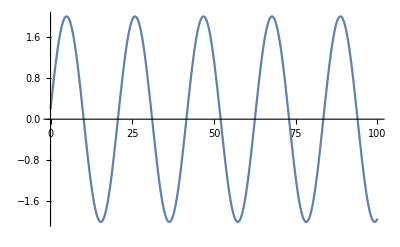

```mathematica
Plot[%, {t, 0, 100}]
```

Obviously you must specifies numerical values for all the parameters, or you can manipulate them...

```mathematica
Manipulate[Plot[A Sin[ω t + ϕ], {t, 0, 100}],{ A, 2, 10}, {ω, 0.3, 1}, {ϕ, 0.1, 10}]
```

You can also manipulate different objects

```mathematica
Manipulate[Factor[x^n+1],{n,10,100,1}]
```

The idea now is to solve some simple (if you have a bachelor degree in physics) physical problems using MATHEMATICA. Doing this we will discover the main feature of this language.
All the exercise in this lessons are taken from [1]. A more exhaustive treatment can be found in this book. A suggested reading.

## Moving object with non-trivial EoM

Consider an object with the following EoM

Find velocity and acceleration. Define the position, velocity and acceleration functions.

Plots these along with the position on a single graph with legends.

Find the time(s) at which there is no net force on the object.

Study the asymptotic regime for large time of the acceleration.

## Gravity near the Earth’s surface

Find an expression up to second order for the modification to g for an object at the height h above the level of the sea (with respect we suppose g has been defined). We need to find a small parameter to expand in series on it.

```mathematica
force = G m M / (R+h)^2
```

(G m M)/(h+R)^2

Express the above expression in term of the usual gravity acceleration g instead of G Newton constant.

## Pendulum period

Consider a very standard pendulum: string of length l with a blob of mass m in the end. We know the period is 2π √(l/g) but this is accurate only if the maximum displacement satisfies θ_0<<1 . How to find an expression for the period as a function of θ_0?

From energy conservation we have that energy at θ = θ_0 is equal to the energy at θ = 0.  Thus

We can reduce this equation to an expression for the angular velocity .

(We choose the minus sign because we’ll be thinking about the quarter period of the pendulum if it is released from rest at , hence the angle is decreasing.
The period is four times the time it takes to go from  to .

This is a scary integral and there is no closed analytic form for it, but it is no problem for MATHEMATICA. Calculate the integral.

Plot the ratio between the period found and the period of a standard pendulum as a function of θ_0. How it behaves in the small angle limit?

## A Falling Ball with Drag

Consider a mass , initially at rest, dropped from a height  and subject to a linear drag force  proportional to the velocity.
Find an expression for its height as a function of time and plot it for various value of .

We need to solve the following differential equation

Find the height as a function of the time for a generic value of b.

Check the b→0 limit

Plot the height as a function of the time varying b with Manipulate.

Find the velocity fuction and study the t→∞ limit.

Plot the velocity function as a function of time for 5 values of the parameter b in a single plot.

## Fourier Series

Consider the function . Obtain and plot the Fourier series of this function. 
Tip: Since it is an odd function only the sine components should be different from zero.

Start finding a generic expression for the Fourier coefficients. List the first 10 coeff.

Plot the series for a tunable number of terms and varies their numbers using Manipulate.

## References

[1] A Mathematica Primer for Physicists, Jim Napolitano
[2] https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html
[3] https://mathematica.stackexchange.com/questions/18393/what-are-the-most-common-pitfalls-awaiting-new-users/25616#25616
[4] https://reference.wolfram.com/language/tutorial/Lists.html#2534
[5] https://demonstrations.wolfram.com/2DWavePropagation/
[6] https://mathematica.stackexchange.com/questions/134609/why-should-i-avoid-the-for-loop-in-mathematica
[7] https://reference.wolfram.com/language/ref/Module.html

```mathematica
Other Links
```

I used these links as a support during the lesson.

- Archives: https://www.wolframphysics.org/archives/index/
- Keyboard Shortcuts: https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html
- Demonstration Projects: https://demonstrations.wolfram.com/
- Wolfram Community: https://community.wolfram.com/
- Wolfram Documentation (First function): https://reference.wolfram.com/language/ref/Find.html?q=Find
- Wolfram syntax: https://mathematica.stackexchange.com/questions/18393/what-are-the-most-common-pitfalls-awaiting-new-users/25616#25616